# Projections

```mathematica
ψ = Sum[c[G]*Exp[ⅈGr],G]/Sqrt[vol];
```

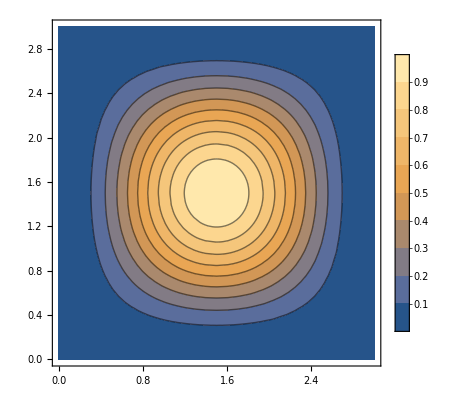

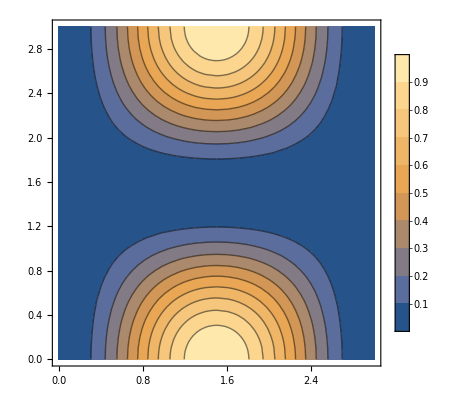

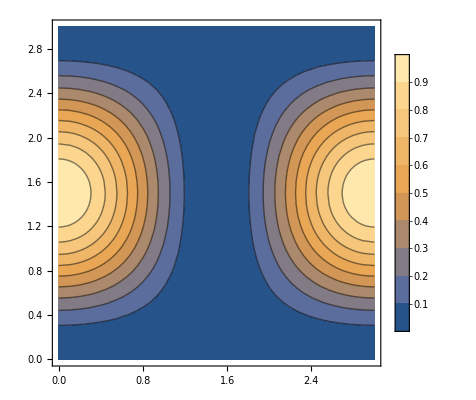

(ⅇ^(-ⅈ Gy (yL+yR)) (-ⅇ^(-ⅈ Gx xL) (κ Cos[xL κ]+ⅈ Gx Sin[xL κ])+ⅇ^(-ⅈ Gx xR) (κ Cos[xR κ]+ⅈ Gx Sin[xR κ])) (-ⅇ^(ⅈ Gy yR) (κ Cos[yL κ]+ⅈ Gy Sin[yL κ])+ⅇ^(ⅈ Gy yL) (κ Cos[yR κ]+ⅈ Gy Sin[yR κ])))/(√vol (Gy-κ) (Gy+κ) (Gx^2-κ^2))

```mathematica
(*Trial Orbitals*)
Clear[L,k];
g1[x_,y_]:=Sin[κ*x]*Sin[κ*y];
g2[x_,y_]:=Sin[κ*x]*Cos[κ*y];
g3[x_,y_]:=Cos[κ*x]*Sin[κ*y];
(*Plane wave basis function (c.c.)*)
basVec[x_,y_,Gx_,Gy_]:= Exp[-ⅈ*(Gx*x+Gy*y)]/Sqrt[vol];

(*Plotting of trial orbitals*)
κ=π/3;
ContourPlot[g1[x,y]^2,{x,0,3},{y,0,3},PlotLegends->Automatic]
ContourPlot[g2[x,y]^2,{x,0,3},{y,0,3},PlotLegends->Automatic]
ContourPlot[g3[x,y]^2,{x,0,3},{y,0,3},PlotLegends->Automatic]

(*Integrals*)
Clear[κ];
Clear[Gx,Gy];
f1[Gx_,Gy_]:= Integrate[basVec[x,y,Gx,Gy]*g1[x,y],{x,xL,xR},{y,yL,yR}];
f2[Gx_,Gy_]:= Integrate[basVec[x,y,Gx,Gy]*g2[x,y],{x,xL,xR},{y,yL,yR}];
f3[Gx_,Gy_]:= Integrate[basVec[x,y,Gx,Gy]*g3[x,y],{x,xL,xR},{y,yL,yR}];

f1[Gx,Gy]
```

## 3 Trial Orbitals per well